## Load packages and global definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../../Mathematica_packages/QMB.wl"]
Get["../../Mathematica_packages/Chaometer.wl"]
```

## Closed XXZ

```mathematica
L=9;(* number of spins *)
Δ=1.;(* anisotropy *)
```

Compute eigenvalues and eigenvectors of Hamiltonian:

```mathematica
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Chop[Eigensystem[ClosedXXZHamiltonian[L,Δ]]]]]];
```

Define an initial random state for the environment (L-1 left-most spins in the chain):

```mathematica
ψE=RandomChainProductState[L-1];
```

```mathematica
AbsoluteTiming[Chop[Superoperator[10,ψE,eigenvalsH,eigenvecsH,L]]]
```

{0.762696,{{0.684546,0.000990532-0.00647305 ⅈ,0.000990532+0.00647305 ⅈ,0.484616},{-0.112394+0.0133224 ⅈ,0.158647+0.0117221 ⅈ,0.0377895+0.0333552 ⅈ,-0.101921+0.0839007 ⅈ},{-0.112394-0.0133224 ⅈ,0.0377895-0.0333552 ⅈ,0.158647-0.0117221 ⅈ,-0.101921-0.0839007 ⅈ},{0.315454,-0.000990532+0.00647305 ⅈ,-0.000990532-0.00647305 ⅈ,0.515384}}}

```mathematica
0.75*50
```

37.5

Compute the superoperator for 0<=t<=50 (Δt=0.1) for every initial environmental state in ψE:

```mathematica
{t0,tf,Δt}={0,10,0.2};
AbsoluteTiming[superoperators=Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L]]&/@Range[t0,tf,Δt];]
```

{35.992,Null}

```mathematica
chois=1/2*Reshuffle/@superoperators;
```

```mathematica
choiPurities=Chop[Purity/@chois];
```

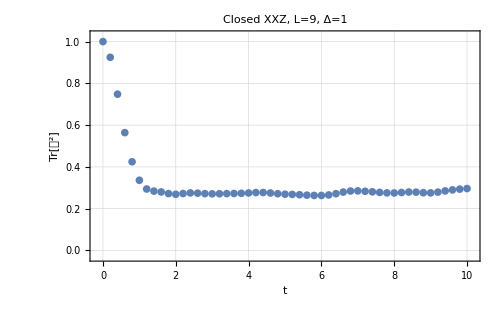

```mathematica
ListPlot[Transpose[{Range[t0,tf,Δt],choiPurities}],
PlotRange->{{t0-0.15,tf+0.15},{-0.03,1.03}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
GridLines->Automatic,
ImageSize->500,
PlotLabel->"Closed XXZ, "<>ToString[TraditionalForm[HoldForm[L=9]]]<>", "<>ToString[TraditionalForm[HoldForm[Δ=1]]],
LabelStyle->Directive[Black,FontSize->17]
]
```

Import data of Wisniacki’s chain:

```mathematica
superoperators=ToExpression[Import["../chaotic/superoperators_1.csv","CSV"][[2;;]]];
```

```mathematica
choisWisniacki=1/2*Reshuffle/@Chop[superoperators];
```

```mathematica
choiPuritiesWisniacki=Purity/@choisWisniacki;
```

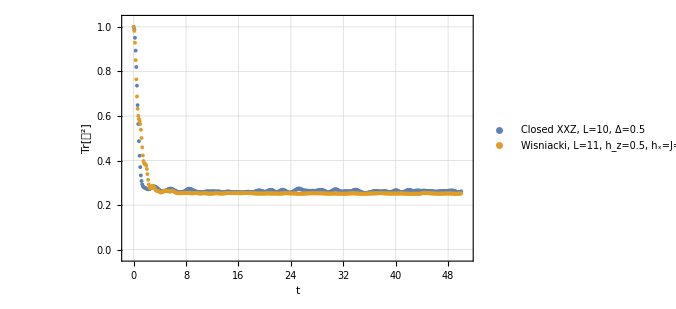

```mathematica
ListPlot[Transpose[{Range[t0,tf,Δt],#}]&/@{choiPurities,choiPuritiesWisniacki},
PlotRange->{{-0.8,50.8},{-0.03,1.03}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
GridLines->Automatic,
ImageSize->500,
PlotLegends->Placed[LineLegend[{"Closed XXZ, "<>ToString[TraditionalForm[HoldForm[L=10]]]<>", "<>ToString[TraditionalForm[HoldForm[Δ=0.5]]],"Wisniacki, L=11, h_z=0.5, h_x=J=1"}],{Right,Top}],
LabelStyle->Directive[Black,FontSize->17]
]
```

Import data of Lipkin’s model:

```mathematica
superoperators=Import["../lipkin/vie_25_oct_2024_1.mx","MX"];
```

```mathematica
choisLipkin=1/2*Map[Reshuffle,superoperators,{2}];
```

```mathematica
choiPuritiesLipkin=Chop[Map[Purity,choisLipkin,{2}]];
```

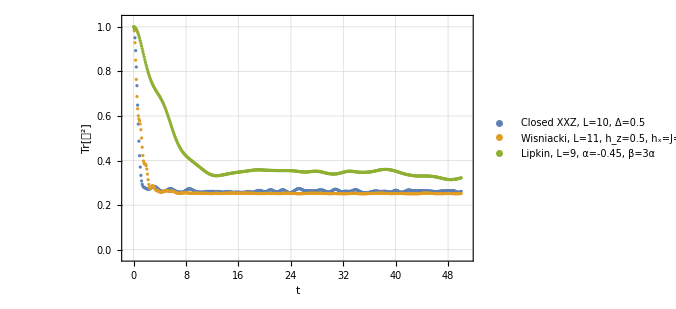

```mathematica
ListPlot[Transpose[{Range[t0,tf,Δt],#}]&/@{choiPurities,choiPuritiesWisniacki,choiPuritiesLipkin[[3]]},
PlotRange->{{-0.8,50.8},{-0.03,1.03}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
GridLines->Automatic,
ImageSize->500,
PlotLegends->Placed[LineLegend[{"Closed XXZ, "<>ToString[TraditionalForm[HoldForm[L=10]]]<>", "<>ToString[TraditionalForm[HoldForm[Δ=0.5]]],"Wisniacki, L=11, h_z=0.5, h_x=J=1","Lipkin, L=9, α=-0.45, β=3α"}],{Right,Top}],
LabelStyle->Directive[Black,FontSize->17]
]
```

```mathematica
{Mean[#],StandardDeviation[#]}&[choiPurities[[40;;]]]
{Mean[#],StandardDeviation[#]}&[choiPuritiesWisniacki[[40;;]]]
{Mean[#],StandardDeviation[#]}&[choiPuritiesLipkin[[3]]]
```

{0.26284,0.0040504}

{0.252993+0. ⅈ,0.00231681}

{0.402152,0.145256}